```mathematica
repFullToNew/.RepEmbed["C"]/.RepEmbed["W"]
```

{0→0,10→10,6→6,20→20,14→14,11→11,31→31,6→6,0→0,10→10,10→10,14→14,10→10,14→14,11→11,11→11,29→29,8→8,16→16,11→11,9→9,3→3,8→8,8→8,4→4,20→20,12→12,9→9,8→8,8→8,3→3,4→4,13→13,5→5,7→7,9→9,16→16,11→11,16→16,8→8,29→29,11→11,21→21,26→26,13→13,5→5,18→18,20→20,12→12,18→18,16→16,16→16}

```mathematica
Table[k->{allGraphs5[k,"jake"],allGraphs5[k,"embed"],(allGraphs5[k,"jake"]/.RepEmbed["W"])},{k,newKeys}]
```

{29524→{w1x2x3x4x5,0,0},29525→{w1x2x3x45,10,10},29527→{w1x2x35x4,6,6},29533→{w1x2x34x5,20,20},29537→{w1x2x345,14,14},29551→{w1x25x3x4,11,11},29560→{w1x25x34,31,31},29605→{w1x24x3x5,6,6},84→{w1x24x35,385,385},29633→{w1x245x3,10,10},29767→{w1x23x4x5,10,10},29768→{w1x23x45,14,14},29797→{w1x235x4,10,10},29857→{w1x234x5,14,14},29888→{w1x2345,11,11},30253→{w15x2x3x4,11,11},30262→{w15x2x34,29,29},30334→{w15x24x3,8,8},30496→{w15x23x4,16,16},30586→{w15x234,11,11},31711→{w14x2x3x5,9,9},2190→{w14x2x35,368,368},2214→{w14x25x3,314,314},31954→{w14x23x5,8,8},31984→{w14x235,4,4},32441→{w145x2x3,20,20},32684→{w145x23,12,12},36085→{w13x2x4x5,9,9},36086→{w13x2x45,8,8},6588→{w13x25x4,314,314},6642→{w13x24x5,368,368},36194→{w13x245,4,4},36817→{w135x2x4,13,13},36898→{w135x24,5,5},38281→{w134x2x5,7,7},38308→{w134x25,9,9},39014→{w1345x2,16,16},49207→{w12x3x4x5,11,11},49208→{w12x3x45,16,16},49210→{w12x35x4,8,8},49216→{w12x34x5,29,29},49220→{w12x345,11,11},49963→{w125x3x4,21,21},49972→{w125x34,26,26},51475→{w124x3x5,13,13},51478→{w124x35,5,5},52232→{w1245x3,18,18},56011→{w123x4x5,20,20},56012→{w123x45,12,12},56770→{w1235x4,18,18},58288→{w1234x5,16,16},59048→{w12345,16,16}}

```mathematica
RepEmbed["W"]
```

{w1x2x3x4x5→385,w1x2x3x4x5→368,w1x2x3x4x5→314,w1x2x3x4x5→314,w1x2x3x4x5→368,w1x2x3x4x5→0,w1x2x3x45→10,w1x2x34x5→20,w1x2x35x4→6,w1x23x4x5→10,w1x24x3x5→6,w1x25x3x4→11,w12x3x4x5→11,w13x2x4x5→9,w14x2x3x5→9,w15x2x3x4→11,w1x2x345→14,w1x23x45→14,w1x234x5→14,w1x235x4→10,w1x245x3→10,w1x25x34→31,w12x3x45→16,w12x34x5→29,w12x35x4→8,w123x4x5→20,w124x3x5→13,w125x3x4→21,w13x2x45→8,w134x2x5→7,w135x2x4→13,w14x23x5→8,w145x2x3→20,w15x2x34→29,w15x23x4→16,w15x24x3→8,w1x2345→11,w12x345→11,w123x45→12,w1234x5→16,w1235x4→18,w124x35→5,w1245x3→18,w125x34→26,w13x245→4,w134x25→9,w1345x2→16,w135x24→5,w14x235→4,w145x23→12,w15x234→11,w12345→16}

```mathematica
Select[Keys[allGraphs5],!KeyExistsQ[allGraphs5[#],"embed"]&]
```

{}

```mathematica
Keys[allGraphs5[0]]//Sort
```

{atleast,atleastwhy,children,colofour,colofourgenerator,colofournull,colofourrealnull,colofourtree,colortable,colotree,comp,compwhy,edges,embed,graph,jake,links,matrix,parents,relations,signature,vertexsets,vertices}

```mathematica
Monitor[Table[allGraphs5[k,"embed2"]=ChromaticPolynomial[EmbedGraphInPlantri8[ allGraphs5,k],4]/24,{k,Sort[Keys[allGraphs5]]}],k];
```

```mathematica
Table[k->{allGraphs5[k,"jake"],allGraphs5[k,"embed2"],allGraphs5[k,"embed"],(allGraphs5[k,"jake"]/.RepEmbed["W"])},{k,newKeys}]
```

{29524→{w1x2x3x4x5,0,0,0},29525→{w1x2x3x45,10,10,10},29527→{w1x2x35x4,6,6,6},29533→{w1x2x34x5,20,20,20},29537→{w1x2x345,14,14,14},29551→{w1x25x3x4,11,11,11},29560→{w1x25x34,31,31,31},29605→{w1x24x3x5,6,6,6},84→{w1x24x35,385,385,385},29633→{w1x245x3,10,10,10},29767→{w1x23x4x5,10,10,10},29768→{w1x23x45,14,14,14},29797→{w1x235x4,10,10,10},29857→{w1x234x5,14,14,14},29888→{w1x2345,11,11,11},30253→{w15x2x3x4,11,11,11},30262→{w15x2x34,29,29,29},30334→{w15x24x3,8,8,8},30496→{w15x23x4,16,16,16},30586→{w15x234,11,11,11},31711→{w14x2x3x5,9,9,9},2190→{w14x2x35,368,368,368},2214→{w14x25x3,314,314,314},31954→{w14x23x5,8,8,8},31984→{w14x235,4,4,4},32441→{w145x2x3,20,20,20},32684→{w145x23,12,12,12},36085→{w13x2x4x5,9,9,9},36086→{w13x2x45,8,8,8},6588→{w13x25x4,314,314,314},6642→{w13x24x5,368,368,368},36194→{w13x245,4,4,4},36817→{w135x2x4,13,13,13},36898→{w135x24,5,5,5},38281→{w134x2x5,7,7,7},38308→{w134x25,9,9,9},39014→{w1345x2,16,16,16},49207→{w12x3x4x5,11,11,11},49208→{w12x3x45,16,16,16},49210→{w12x35x4,8,8,8},49216→{w12x34x5,29,29,29},49220→{w12x345,11,11,11},49963→{w125x3x4,21,21,21},49972→{w125x34,26,26,26},51475→{w124x3x5,13,13,13},51478→{w124x35,5,5,5},52232→{w1245x3,18,18,18},56011→{w123x4x5,20,20,20},56012→{w123x45,12,12,12},56770→{w1235x4,18,18,18},58288→{w1234x5,16,16,16},59048→{w12345,16,16,16}}

```mathematica
Bases["W","Variables"]//DeleteDuplicates//Length
```

52

```mathematica
allGraphs5[84,"jake"]
```

w1x24x35

```mathematica
allGraphs5[29524,"jake"]
```

w1x2x3x4x5

```mathematica
RepEmbed["W"]
```

{w1x2x3x4x5→385,w1x2x3x4x5→368,w1x2x3x4x5→314,w1x2x3x4x5→314,w1x2x3x4x5→368,w1x2x3x4x5→0,w1x2x3x45→10,w1x2x34x5→20,w1x2x35x4→6,w1x23x4x5→10,w1x24x3x5→6,w1x25x3x4→11,w12x3x4x5→11,w13x2x4x5→9,w14x2x3x5→9,w15x2x3x4→11,w1x2x345→14,w1x23x45→14,w1x234x5→14,w1x235x4→10,w1x245x3→10,w1x25x34→31,w12x3x45→16,w12x34x5→29,w12x35x4→8,w123x4x5→20,w124x3x5→13,w125x3x4→21,w13x2x45→8,w134x2x5→7,w135x2x4→13,w14x23x5→8,w145x2x3→20,w15x2x34→29,w15x23x4→16,w15x24x3→8,w1x2345→11,w12x345→11,w123x45→12,w1234x5→16,w1235x4→18,w124x35→5,w1245x3→18,w125x34→26,w13x245→4,w134x25→9,w1345x2→16,w135x24→5,w14x235→4,w145x23→12,w15x234→11,w12345→16}

```mathematica
allGraphs5[29524]
```

<|signature→29524,matrix→{{2,1,1,1,1},{1,2,1,1,1},{1,1,2,1,1},{1,1,1,2,1},{1,1,1,1,2}},graph→-Graphics-,vertexsets→{{1},{2},{3},{4},{5}},vertices→{1,2,3,4,5},edges→{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5},relations→{x29524==x29523-x29525,x29524==x29521-x29527,x29524==x29515-x29533,x29524==x29497-x29551,x29524==x29443-x29605,x29524==x29281-x29767,x29524==x28795-x30253,x29524==x27337-x31711,x29524==x22963-x36085,x29524==-x49207+x9841},links→{},parents→{29523,29521,29515,29497,29443,29281,28795,27337,22963,9841},children→{},comp→Equal,compwhy→This graph contains Clique of size5,colofour→v1x2x3x4x5,colortable→{{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5},{0,v1x2x3x4x5}},colofournull→p12345,colofourrealnull→24 n12345-6 n1234x5-6 n1235x4-2 n123x45+2 n123x4x5-6 n1245x3-2 n124x35+2 n124x3x5-2 n125x34+2 n125x3x4-2 n12x345+n12x34x5+n12x35x4+n12x3x45-n12x3x4x5-6 n1345x2-2 n134x25+2 n134x2x5-2 n135x24+2 n135x2x4-2 n13x245+n13x24x5+n13x25x4+n13x2x45-n13x2x4x5-2 n145x23+2 n145x2x3-2 n14x235+n14x23x5+n14x25x3+n14x2x35-n14x2x3x5-2 n15x234+n15x23x4+n15x24x3+n15x2x34-n15x2x3x4-6 n1x2345+2 n1x234x5+2 n1x235x4+n1x23x45-n1x23x4x5+2 n1x245x3+n1x24x35-n1x24x3x5+n1x25x34-n1x25x3x4+2 n1x2x345-n1x2x34x5-n1x2x35x4-n1x2x3x45+n1x2x3x4x5,atleast→0,atleastwhy→All graphs are at least zero,embed→0,colofourgenerator→g1x2x3x4x5,colofourtree→-t49194+t49196+t49200+t49212-2 t49220-4 t58288-2 t7034-4 t7480-4 t7647+4 t7704+4 t778-4 t840+2 t8436+4 t846-2 t8778+2 t8797+2 t8856+2 t8884-2 t9048-2 t9117+t9504-t9522-t9558-t9564+t9720-t9722-2 t9753+8 t9854,colotree→-6 t1345x2+2 t134x2x5+2 t135x2x4+t13x25x4-t13x2x4x5+2 t145x2x3+t14x25x3-t14x2x3x5+t15x24x3-t15x2x3x4+2 t1x245x3-t1x24x3x5-t1x25x3x4-t1x2x35x4+t1x2x3x4x5,jake→w1x2x3x4x5,embed2→0|>

```mathematica
Select[Keys[allGraphs5],allGraphs5[#,"embed"]!=allGraphs5[#,"embed2"]&]
```

{}

```mathematica
BaseCoeff[0,"W"]
```

{-3/2,-3/2,-3/2,-1/2,-3/2,-1/2,-1/2,-3/2,-1/2,-1/2,-3/2,-1/2,-3/2,-1/2,1/2,1/2,1/2,-1/2,-3/2,-3/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2,1/2,1/2,1/2,-1/2,1/2,-1/2,-3/2,-3/2,-1/2,1,-1/2,-1/2,1,1,1/2,1,-1/2,1/2,1/2,1,1/2,1/2,-1/2,-1/2,1}

```mathematica
BaseCoeff[lambdaKey,"W"]
```

{-3/2,-5/2,-5/2,-1/2,-5/2,-1/2,-1/2,-5/2,-1/2,-1/2,-5/2,-3/2,-5/2,-3/2,-1/2,1/2,-1/2,-3/2,-5/2,-5/2,-3/2,-3/2,-1/2,-3/2,-3/2,1/2,1/2,-1/2,-1/2,1/2,-3/2,1/2,-3/2,-5/2,-5/2,-3/2,0,-3/2,-3/2,0,0,-1/2,0,-3/2,-1/2,-1/2,0,-1/2,-1/2,-3/2,-3/2,0}

```mathematica
BaseCoeff[K5Key,"W"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[BaseCoeff[k,"W"].BaseCoeff[l,"W"],{k,quads},{l,alfa1s}]+1/2//MatrixForm
```

(0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

```mathematica
quads2=Map[quads[[#]]&,{1,3,5,2,4}]
```

{36085,29527,29551,29605,31711}

```mathematica
Table[ShowGraph5Least[k],{k,quads2}]
```

{-Graphics-360850,-Graphics-295270,-Graphics-295510,-Graphics-296050,-Graphics-317110}

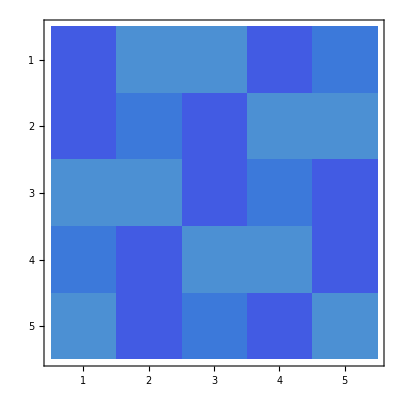
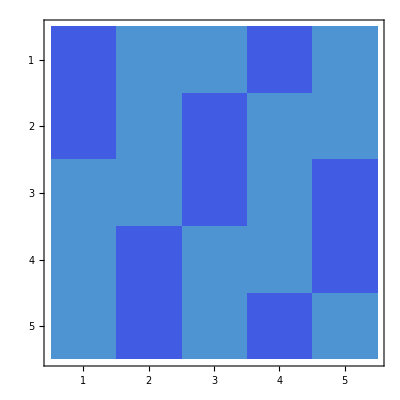
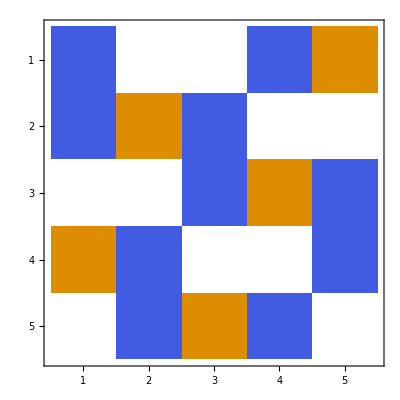
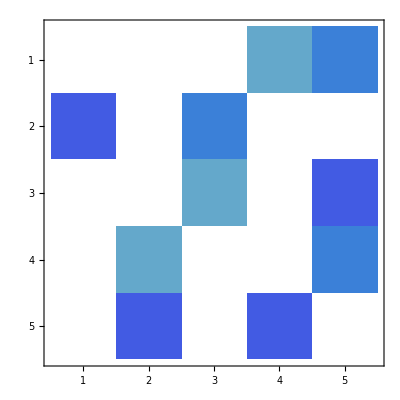
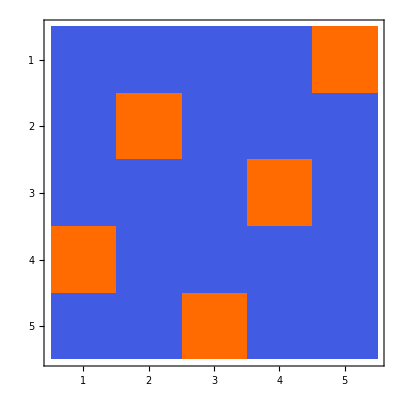
{-Graphics-C,-Graphics-E,-Graphics-G,-Graphics-F,-Graphics-T,-Graphics-W}

```mathematica
Table[Labeled[Table[BaseCoeff[k,base].BaseCoeff[l,base],{k,quads},{l,alfa1s}]//MatrixPlot,base],
{base,allBases}]
```

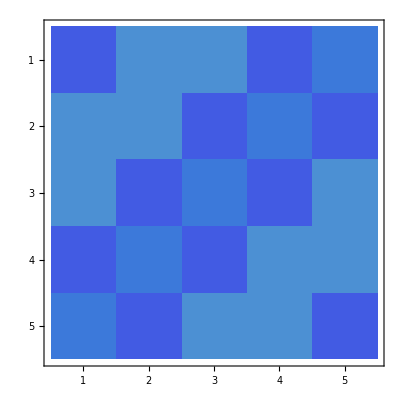
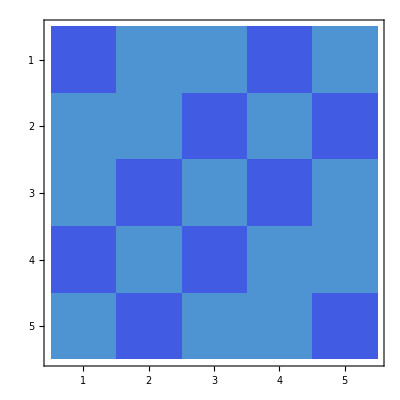
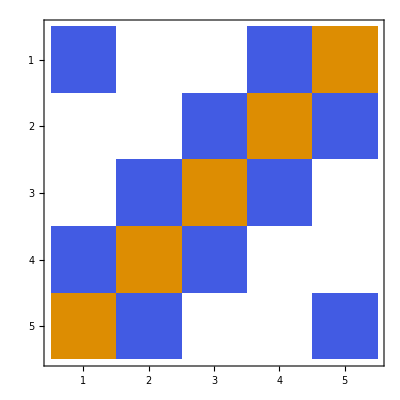
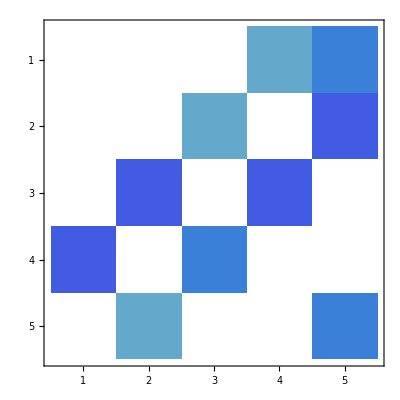
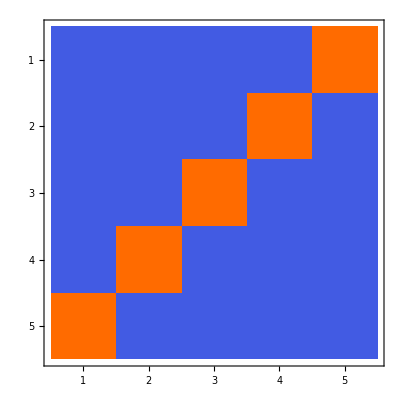
{-Graphics-C,-Graphics-E,-Graphics-G,-Graphics-F,-Graphics-T,-Graphics-W}

```mathematica
Table[Labeled[Table[BaseCoeff[k,base].BaseCoeff[l,base],{k,quads2},{l,alfa1s}]//MatrixPlot,base],
{base,allBases}]
```

```mathematica
Table[Labeled[Table[BaseCoeff[k,base].BaseCoeff[l,base],{k,{lambdaKey,K5Key,0}},{l,alfa1s}]//MatrixForm,base],
{base,allBases}]
```

{(1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1)C,(9 | 9 | 9 | 9 | 9
59 | 59 | 59 | 59 | 59
0 | 0 | 0 | 0 | 0)E,(4 | 4 | 4 | 4 | 4
1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0)G,(-1/18 | -1/18 | -1/18 | -1/18 | -1/18
1/12 | 1/12 | 1/12 | 1/12 | 1/12
0 | 0 | 0 | 0 | 0)F,(0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 6
0 | 0 | 0 | 0 | 0)T,(43/2 | 43/2 | 43/2 | 43/2 | 43/2
-1/2 | -1/2 | -1/2 | -1/2 | -1/2
11 | 11 | 11 | 11 | 11)W}

```mathematica
With[
{base="W"},
Table[
Length[Select[Keys[allGraphs5],BaseCoeff[k,base].BaseCoeff[#,base]==0&]]
,{k,Bases["W","AtomKeys"]}]
]
```

{751,783,783,1039,783,1039,1039,783,1039,1039,783,967,823,967,1063,1135,1063,999,823,823,999,967,1063,967,999,1135,1135,1063,1063,1135,999,1135,967,823,823,999,1801,981,981,1801,1801,1117,1801,981,1117,1117,1801,1117,1117,981,981,1843}

```mathematica
Monitor[Table[
Table[
Length[Select[Keys[allGraphs5],BaseCoeff[k,base].BaseCoeff[#,base]==0&]]
,{k,Bases[base,"AtomKeys"]}],
{base,allBases}
],{k,base}]
```

{{871,1319,1319,1319,1319,1319,1319,1319,1319,1319,1319,1663,1567,1663,1663,1567,1663,1567,1567,1567,1567,1663,1663,1663,1567,1567,1567,1663,1663,1567,1567,1567,1663,1567,1567,1567,1801,1757,1757,1801,1801,1757,1801,1757,1757,1757,1801,1757,1757,1757,1757,1843},{871,1319,1319,1319,1319,1319,1319,1319,1319,1319,1319,1279,1567,1279,1279,1567,1279,1567,1567,1567,1567,1279,1279,1279,1567,1567,1567,1279,1279,1567,1567,1567,1279,1567,1567,1567,1065,1541,1541,1065,1065,1541,1065,1541,1541,1541,1065,1541,1541,1541,1541,671},{526,1199,1199,1199,1199,1199,1199,1199,1199,1199,1199,1635,1528,1635,1635,1528,1635,1528,1528,1528,1528,1635,1635,1635,1528,1528,1528,1635,1635,1528,1528,1528,1635,1528,1528,1528,1779,1725,1725,1779,1779,1725,1779,1725,1725,1725,1779,1725,1725,1725,1725,1843},{1843,684,684,684,684,684,684,684,684,684,684,767,824,767,767,824,767,824,824,824,824,767,767,767,824,824,824,767,767,824,824,824,767,824,824,824,692,668,668,692,692,668,692,668,668,668,692,668,668,668,668,671},{871,1319,1319,1319,1319,1319,1319,1319,1319,1319,1319,1663,1567,1663,1407,1567,1279,1567,1567,1567,1567,1663,1407,1407,1567,1567,1567,1279,1279,1567,1567,1567,1279,1567,1567,1567,1801,1757,1757,1801,1657,1613,1329,1613,1757,1541,1065,1541,1757,1541,1757,1843},{751,783,783,1039,783,1039,1039,783,1039,1039,783,967,823,967,1063,1135,1063,999,823,823,999,967,1063,967,999,1135,1135,1063,1063,1135,999,1135,967,823,823,999,1801,981,981,1801,1801,1117,1801,981,1117,1117,1801,1117,1117,981,981,1843}}

```mathematica
Total[{871,1319,1319,1319,1319,1319,1319,1319,1319,1319,1319,1663,1567,1663,1663,1567,1663,1567,1567,1567,1567,1663,1663,1663,1567,1567,1567,1663,1663,1567,1567,1567,1663,1567,1567,1567,1801,1757,1757,1801,1801,1757,1801,1757,1757,1757,1801,1757,1757,1757,1757,1843}]
```

82614

```mathematica
Total[{871,1319,1319,1319,1319,1319,1319,1319,1319,1319,1319,1279,1567,1279,1279,1567,1279,1567,1567,1567,1567,1279,1279,1279,1567,1567,1567,1279,1279,1567,1567,1567,1279,1567,1567,1567,1065,1541,1541,1065,1065,1541,1065,1541,1541,1541,1065,1541,1541,1541,1541,671}]
```

71762

```mathematica
perPart=Association[];
```

```mathematica
Table[perPart[k]={},{k,SetPartitions[Range[5]]}]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Table[With[{part=allGraphs5[k,"vertexsets"]},perPart[part]=Append[perPart[part],k]],{k,Keys[allGraphs5]}]
```

{{0},{0,19683},1892,{29525,29513,29417,29405,29282,29270,29174,29162,26609,26597,26501,26489,26366,26354,26258,26246,22964,22952,22856,22844,22721,22709,22613,22601,20048,20036,19940,19928,19805,19793,19697,19685,9842,9830,9734,9722,9599,9587,9491,9479,6926,6914,6818,6806,6683,6671,6575,6563,3281,3269,3173,3161,3038,3026,2930,2918,365,353,257,245,122,110,14,2}}
 |  |  |  |

```mathematica
Table[Length[perPart[k]],{k,Keys[perPart]}]
```

{1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,64,64,64,64,64,64,64,64,64,64,1024}

```mathematica
Monitor[Table[
base->Table[
With[{part=allGraphs5[k,"vertexsets"]},
Length[Select[perPart[part],BaseCoeff[k,base].BaseCoeff[#,base]==0&]]
]
,{k,Bases[base,"AtomKeys"]}],
{base,allBases}
],{k,base}]
```

{C→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},E→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},G→{416,732,732,732,732,732,732,732,732,732,732,960,868,960,960,868,960,868,868,868,868,960,960,960,868,868,868,960,960,868,868,868,960,868,868,868,1009,961,961,1009,1009,961,1009,961,961,961,1009,961,961,961,961,1023},F→{1023,381,381,381,381,381,381,381,381,381,381,387,441,387,387,441,387,441,441,441,441,387,387,387,441,441,441,387,387,441,441,441,387,441,441,441,331,305,305,331,331,305,331,305,305,305,331,305,305,305,305,296},T→{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},W→{160,0,0,16,0,16,16,0,16,16,0,0,0,0,0,480,0,0,0,0,0,0,0,0,0,480,480,0,0,480,0,480,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
With[{base1="G",base2="G"},
Table[
With[{part=allGraphs5[k,"vertexsets"]},
Length[Select[perPart[part],BaseCoeff[k,base1].BaseCoeff[#,base2]==0&]]
]
,{k,Bases[base1,"AtomKeys"]}]
]
```

{416,732,732,732,732,732,732,732,732,732,732,960,868,960,960,868,960,868,868,868,868,960,960,960,868,868,868,960,960,868,868,868,960,868,868,868,1009,961,961,1009,1009,961,1009,961,961,961,1009,961,961,961,961,1023}

```mathematica
Table[Length[Select[perPart[k],allGraphs5[#,"atleast"]>0&]]/Length[perPart[k]],{k,Keys[perPart]}]
```

{1,1,1,1,1,1,1,1/2,1,1,1,1/2,1,1/2,1/2,1/2,1,1,7/8,1,7/8,7/8,1/2,1,7/8,1,1,7/8,1,7/8,7/8,1/2,1,7/8,1,7/8,1/2,7/8,1,1/2,1/2,63/64,63/64,49/64,63/64,49/64,49/64,63/64,49/64,49/64,63/64,469/512}

```mathematica
allGraphs5[0,"colofournull"]
```

p1x2x3x4x5

```mathematica
TableForm[
Sort[
Table[(PartitionToSymbol[ k,"v"]/.RepGraph["C"])->Map[Labeled[ShowGraph5Least[#],allGraphs5[#,"embed"]]&,
Sort[
Select[perPart[k],allGraphs5[#,"atleast"]==0&],
allGraphs5[#1,"embed"]>allGraphs5[#2,"embed"]&
]
],{k,Keys[perPart]}],
Length[#1[[2]]]>Length[#2[[2]]]&]]
```

-Graphics-295240→{-Graphics-22708045,-Graphics-27246045,-Graphics-364040,-Graphics-3253039,-Graphics-7627039,-Graphics-22207039,-Graphics-22711039,-Graphics-26581039,-Graphics-27327039,-Graphics-9490038,-Graphics-22693038,-Graphics-22873038,-Graphics-27309038,-Graphics-27325038,-Graphics-28764038,-Graphics-29269036,-Graphics-29433036,-Graphics-22951035,-Graphics-27247035,-Graphics-9571032,-Graphics-28767032,-Graphics-29431032,-Graphics-2551031,-Graphics-6925031,-Graphics-29272030,-Graphics-29514030,-Graphics-1093029,-Graphics-3199029,-Graphics-20047029,-Graphics-22954029,-Graphics-26605029,-Graphics-27328029,-Graphics-9733028,-Graphics-22639028,-Graphics-22936028,-Graphics-27310028,-Graphics-27333028,-Graphics-28765028,-Graphics-9517027,-Graphics-28791027,-Graphics-29173027,-Graphics-29493027,-Graphics-29434026,-Graphics-29512026,-Graphics-22717025,-Graphics-27255025,-Graphics-9112022,-Graphics-9814022,-Graphics-28768022,-Graphics-29197022,-Graphics-29439022,-Graphics-9598021,-Graphics-28794021,-Graphics-29254021,-Graphics-29496021,-Graphics-3280020,-Graphics-7654020,-Graphics-22234020,-Graphics-26608020,-Graphics-29515020,-Graphics-22720019,-Graphics-27336019,-Graphics-20776018,-Graphics-22882018,-Graphics-27334018,-Graphics-9760017,-Graphics-28792017,-Graphics-29416017,-Graphics-29494017,-Graphics-29200016,-Graphics-29278016,-Graphics-29442016,-Graphics-29520016,-Graphics-22960015,-Graphics-27256015,-Graphics-29440012,-Graphics-9841011,-Graphics-28795011,-Graphics-29497011,-Graphics-29281010,-Graphics-29523010,-Graphics-2296309,-Graphics-2733709,-Graphics-2944306,-Graphics-2952106,-Graphics-2952400}
-Graphics-317110→{-Graphics-11677038,-Graphics-11704030,-Graphics-11920030,-Graphics-5377029,-Graphics-24895027,-Graphics-31441025,-Graphics-24898024,-Graphics-11947022,-Graphics-31465020,-Graphics-25138019,-Graphics-31468017,-Graphics-31684017,-Graphics-25141016,-Graphics-31708012,-Graphics-3171109}
-Graphics-360850→{-Graphics-35325038,-Graphics-35326030,-Graphics-35352030,-Graphics-33157029,-Graphics-33807027,-Graphics-36057025,-Graphics-33888024,-Graphics-35353022,-Graphics-36003020,-Graphics-33808019,-Graphics-36058017,-Graphics-36084017,-Graphics-33889016,-Graphics-36004012,-Graphics-3608509}
-Graphics-295510→{-Graphics-22735060,-Graphics-27273060,-Graphics-29296052,-Graphics-29460052,-Graphics-22981050,-Graphics-27355050,-Graphics-29542042,-Graphics-29223031,-Graphics-22744029,-Graphics-27282029,-Graphics-29305021,-Graphics-29469021,-Graphics-22990019,-Graphics-27364019,-Graphics-29551011}
-Graphics-296050→{-Graphics-445030,-Graphics-7707029,-Graphics-7006027,-Graphics-28848024,-Graphics-28845024,-Graphics-1174022,-Graphics-7735019,-Graphics-22315017,-Graphics-29577016,-Graphics-29574016,-Graphics-28876014,-Graphics-28873014,-Graphics-2304409,-Graphics-2960506,-Graphics-2960206}
-Graphics-295270→{-Graphics-367030,-Graphics-21967029,-Graphics-2554027,-Graphics-9493024,-Graphics-9574024,-Graphics-20050022,-Graphics-22237019,-Graphics-7657017,-Graphics-29176016,-Graphics-29257016,-Graphics-9763014,-Graphics-9844014,-Graphics-2734009,-Graphics-2944606,-Graphics-2952706}
-Graphics-317380→{-Graphics-24922021,-Graphics-25168017,-Graphics-31492012,-Graphics-3173808}
-Graphics-361120→{-Graphics-33834021,-Graphics-33916017,-Graphics-36030012,-Graphics-3611208}
-Graphics-361660→{-Graphics-35406012,-Graphics-3543408,-Graphics-3613807,-Graphics-3616603}
-Graphics-317140→{-Graphics-11680012,-Graphics-1195008,-Graphics-3144407,-Graphics-3171403}
-Graphics-296080→{-Graphics-448010,-Graphics-773805,-Graphics-2231805,-Graphics-2960800}
-Graphics-302530→{-Graphics-30253011}
-Graphics-492070→{-Graphics-49207011}
-Graphics-297670→{-Graphics-29767010}
-Graphics-295330→{-Graphics-29533020}
-Graphics-295250→{-Graphics-29525010}
-Graphics-303340→{-Graphics-3033408}
-Graphics-514750→{-Graphics-51475013}
-Graphics-319540→{-Graphics-3195408}
-Graphics-368170→{-Graphics-36817013}
-Graphics-492100→{-Graphics-4921008}
-Graphics-382810→{-Graphics-3828107}
-Graphics-360860→{-Graphics-3608608}
-Graphics-297970→{-Graphics-29797010}
-Graphics-295600→{-Graphics-29560031}
-Graphics-296330→{-Graphics-29633010}
-Graphics-368980→{-Graphics-3689805}
-Graphics-514780→{-Graphics-5147805}
-Graphics-319840→{-Graphics-3198404}
-Graphics-383080→{-Graphics-3830809}
-Graphics-361940→{-Graphics-3619404}
-Graphics-499631→{}
-Graphics-304961→{}
-Graphics-560111→{}
-Graphics-302621→{}
-Graphics-492161→{}
-Graphics-324411→{}
-Graphics-492081→{}
-Graphics-298571→{}
-Graphics-297681→{}
-Graphics-295371→{}
-Graphics-567701→{}
-Graphics-499721→{}
-Graphics-305861→{}
-Graphics-582881→{}
-Graphics-522321→{}
-Graphics-326841→{}
-Graphics-560121→{}
-Graphics-390141→{}
-Graphics-492201→{}
-Graphics-298881→{}
-Graphics-590481→{}